## Continuous Curvature Profile w 3 Parabolic Segments

```mathematica
f[x_]:=Piecewise[{{x^2,0<=x<1},{-(x-2)^2+2,1<=x<3},{(x-4)^2,3<=x<4}}]
```

```mathematica
cps=Module[{xs={0,1,2,3,4},ys},
ys=f/@xs;
MapThread[{#1,#2}&,{xs,ys}]];
```

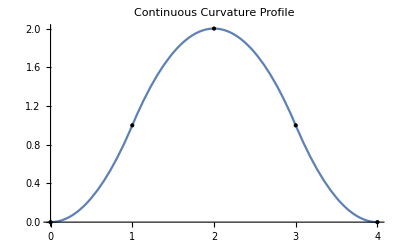

```mathematica
Plot[f[x],{x,0,4},Exclusions->None,Epilog->{PointSize[Medium],Point[cps]},PlotLabel->"Continuous Curvature Profile"]
```

## Integrate Curvature to Get Plane Curve

```mathematica
th[s_]=Integrate[f[x],{x,0,s},Assumptions->s>0]
```

Piecewise[{{4, s>4}, {s^3/3, s≤1}, {1/3 (2-6 s+6 s^2-s^3), 1<s≤3}, {1/3 (-52+48 s-12 s^2+s^3), True}}]

```mathematica
ss=Module[{xs={0,1,2,3,4},ys},
ys=th/@xs;
MapThread[{#1,#2}&,{xs,ys}]];
```

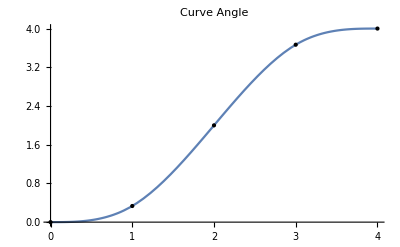

```mathematica
Plot[th[s],{s,0,4},Exclusions->None,Epilog->{PointSize[Medium],Point[ss]},PlotLabel->"Curve Angle"]
```

note: to compute curve angle,curvature will be scaled by constant  """"a"""": k(s) = a *f(x)

```mathematica
Clear[thexy];thexy[a_,s_]:=Module[{t},NIntegrate[t=a th[x];{Cos[t],Sin[t]},{x,0,s}]];
```

## Draw and Interact w/ Integrated Plane Curve, 0<s<4, varying curvature scale factor “a”

```mathematica
oneFr[a_]:=Module[{xys,lab,xmin=-.5,xmax=4,ymin=-.5,ymax=3,xtks,ytks,curveStep=.1},
xys=Table[thexy[a,s],{s,0,4,curveStep}]//Chop;
lab=Style["a = "<>ToString[NumberForm[a,{3,2}]],Large];
xtks=Table[x,{x,xmin,xmax,.5}];
ytks=Table[x,{x,ymin,ymax,.5}];
Graphics[{
{Thick,Darker[Red],Line[xys]},
{Blue,PointSize[Large],Point[thexy[a,#]&/@{0,1,2,3,4}]}
},
ImageSize->Large,
PlotRange->{{xmin,xmax},{ymin,ymax}},
Frame->True,
FrameTicks->{{ytks,None},{xtks,None}},
FrameStyle->Medium,
AspectRatio->Automatic,
GridLines->Automatic,
GridLinesStyle->LightGray,
PlotLabel->lab]];
```

```mathematica
Manipulate[Module[{gr},
gr=oneFr[a];
gr],{{a,.5},0.01,1,.01}]
```

## Export Animated Frames

```mathematica
frs=Table[oneFr[a],{a,.01,2,.01}];
```

```mathematica
Export["integrated curvature.gif",Join[frs,Most[Reverse[frs]]],Options->{"Loop"->True}]
```

integrated curvature.gif